## Haplotypes and fitness

```mathematica
Clear["Global`*"]
```

```mathematica
makegenotype[hmat_,hpat_]:=Sort[Join[hmat,hpat]]
```

```mathematica
haplotypesF={{X,Af},{X,Am},{Xd,Af},{Xd,Am}};
```

```mathematica
haplotypesM={{X,Af},{X,Am},{Xd,Af},{Xd,Am},{Y}};
```

```mathematica
makegenotype[haplotypesF[[1]],haplotypesM[[5]]]
```

{Af,X,Y}

```mathematica
w[genotype_]:=Module[{sex,nxd,naf,w},
sex=If[Length[genotype]==4,f,m];
nxd=Count[genotype,Xd];
naf=Count[genotype,Af];
w=If[Count[{sex},f]==1,
{1-tf,1-h tf,1}[[1+naf]]*{1,1,1-cf}[[1+nxd]],
{1,1-tm}[[1+naf]]*{1,1-cm}[[1+nxd]]
];
Return[w]
]
```

```mathematica
segregation[hapNumMom_,hapNumDad_,hapNumGoal_]:=Module[{haploMom,haploDad,haploGoal,haploRec,haploNoRec,isFemale,hasDrive},
(* see what haplotypes we have *)
haploMom=haplotypesF[[hapNumMom]];
haploDad=haplotypesM[[hapNumDad]];
isFemale=haploDad!={Y};
hasDrive=Count[haploMom,Xd]==1;

(* what haplotype is desired *)
haploGoal=haplotypesM[[hapNumGoal]];

(* possible haplotypes in gametes when no recombination *)
haploNoRec={haploMom,haploDad};

(* we don't need to go through recombination if male *)
If[!isFemale,
Return[
If[hasDrive,If[Count[haploGoal,Y]==1,1-kdrive,kdrive],1/2]*Count[haploNoRec,haploGoal]
]
];

(* possible haplotypes in gametes with recombination *)
haploRec={{haploMom[[1]],haploDad[[2]]},{haploDad[[1]],haploMom[[2]]}};
Return[Simplify[Count[haploNoRec,haploGoal]/2 (1-r)+Count[haploRec,haploGoal]/2 r]]
]
```

## Recursions

Expression for W̄×y_(i,t+1):

```mathematica
WbarMytplus1=
Table[
Sum[
x[i]y[j]w[haplotypesF[[i]]]segregation[i,j,k],{i,1,Length[haplotypesF]},{j,5,5}
],{k,1,Length[haplotypesM]}
];
```

```mathematica
WbarMytplus1
```

{1/2 (1-tm) x[1] y[5],1/2 x[2] y[5],(1-cm) kdrive (1-tm) x[3] y[5],(1-cm) kdrive x[4] y[5],1/2 (1-tm) x[1] y[5]+1/2 x[2] y[5]+(1-cm) (1-kdrive) (1-tm) x[3] y[5]+(1-cm) (1-kdrive) x[4] y[5]}

```mathematica
WbarM=Total[WbarMytplus1];
```

```mathematica
ytplus1=WbarMytplus1/WbarM//Simplify;
```

```mathematica
WbarFxtplus1=Table[
Sum[
x[i]y[j]w[makegenotype[haplotypesF[[i]],haplotypesM[[j]]]]segregation[i,j,k],
{j,1,Length[haplotypesF]},{i,1,Length[haplotypesF]}
],
{k,1,Length[haplotypesF]}
];
```

```mathematica
WbarF=Total[WbarFxtplus1];
```

```mathematica
xtplus1=WbarFxtplus1/WbarF//Simplify;
```

```mathematica
WbarFxtplus1[[1]]
```

x[1] y[1]+1/2 (1-h tf) x[2] y[1]+1/2 x[3] y[1]+1/2 (1-r) (1-h tf) x[4] y[1]+1/2 (1-h tf) x[1] y[2]+1/2 r (1-h tf) x[3] y[2]+1/2 x[1] y[3]+1/2 r (1-h tf) x[2] y[3]+1/2 (1-r) (1-h tf) x[1] y[4]

```mathematica
primarySR=y[5]/(y[5]+Sum[x[i]y[j],{i,1,Length[haplotypesF]},{j,1,Length[haplotypesM]-1}]);
secondarySR=Sum[x[i]y[5]w[haplotypesF[[i]]],{i,1,Length[haplotypesF]}]/(Sum[x[i]y[5]w[haplotypesF[[i]]],{i,1,Length[haplotypesF]}]+Sum[x[i]y[j]w[makegenotype[haplotypesF[[i]],haplotypesM[[j]]]],{i,1,Length[haplotypesF]},{j,1,Length[haplotypesM]-1}]);
```

## Numerical analysis (auxiliary functions)

```mathematica
iterate[{tfs_,tms_,hs_},{cfs_,cms_},{kdrives_,rs_},maxt_]:=Module[{DataX,DataY,xtp1,ytp1,ysub,xsub,parsub,DataSR,srs},
(* allocate data *)
DataY=ConstantArray[Join[{1/Length[haplotypesM]},ConstantArray[0,maxt]],Length[haplotypesM]];
DataX=ConstantArray[Join[{1/Length[haplotypesF]},ConstantArray[0,maxt]],Length[haplotypesF]];
DataSR=ConstantArray[ConstantArray[0,maxt+1],2];

parsub={tf->tfs,tm->tms,h->hs,cf->cfs,cm->cms,kdrive->kdrives,r->rs};
xtp1=xtplus1/.parsub;
ytp1=ytplus1/.parsub;
srs={primarySR,secondarySR}/.parsub;

For[iter=2,iter≤maxt+1,iter++,
ysub=Table[y[i]->DataY[[i,iter-1]],{i,1,Length[haplotypesM]}];
xsub=Table[x[i]->DataX[[i,iter-1]],{i,1,Length[haplotypesF]}];
DataX[[All,iter]]=xtp1/.ysub/.xsub;
DataY[[All,iter]]=ytp1/.ysub/.xsub;
DataSR[[All,iter]]=srs/.ysub/.xsub;
];
Return[Join[DataX,DataY,DataSR]]
]
```

## Export to C

```mathematica
str="";
```

```mathematica
For[iter=1,iter≤Length[xtplus1],iter++,
str=str<>"xtp"<>ToString[iter]<>" = "<>ToString[CForm[xtplus1[[iter]]]]<>";\n\n";
];
For[iter=1,iter≤Length[ytplus1],iter++,
str=str<>"ytp"<>ToString[iter]<>" = "<>ToString[CForm[ytplus1[[iter]]]]<>";\n\n";
];
str=str<>"psr = "<>ToString[CForm[primarySR]]<>";\n\n";
str=str<>"ssr = "<>ToString[CForm[secondarySR]]<>";\n\n";
```

```mathematica
Export[$HomeDirectory<>"/Projects/drive/src/numerical/drive_expressions.txt",str]
```

/home/bram/Projects/drive/src/numerical/drive_expressions.txt

## Results

```mathematica
out=iterate[{0,0,.5},{0.2,0.3},{0.95,0.5},153];
```

```mathematica
out//MatrixForm
```

(1/4 | 0.263158 | 0.252531 | 0.253742 | 0.249305 | 0.247787 | 0.244991 | 0.242962 | 0.240698 | 0.238682 | 0.236674 | 0.234784 | 0.232955 | 0.23121 | 0.229533 | 0.227927 | 0.226387 | 0.22491 | 0.223495 | 0.222138 | 0.220838 | 0.219591 | 0.218395 | 0.217249 | 0.216149 | 0.215095 | 0.214085 | 0.213116 | 0.212186 | 0.211295 | 0.21044 | 0.209619 | 0.208833 | 0.208078 | 0.207354 | 0.206659 | 0.205993 | 0.205353 | 0.20474 | 0.204151 | 0.203586 | 0.203043 | 0.202523 | 0.202023 | 0.201543 | 0.201083 | 0.200641 | 0.200217 | 0.199809 | 0.199418 | 0.199042 | 0.198682 | 0.198336 | 0.198003 | 0.197684 | 0.197377 | 0.197083 | 0.1968 | 0.196528 | 0.196267 | 0.196017 | 0.195776 | 0.195545 | 0.195322 | 0.195109 | 0.194904 | 0.194707 | 0.194518 | 0.194336 | 0.194162 | 0.193994 | 0.193833 | 0.193678 | 0.193529 | 0.193386 | 0.193248 | 0.193116 | 0.192989 | 0.192867 | 0.19275 | 0.192638 | 0.192529 | 0.192425 | 0.192326 | 0.192229 | 0.192137 | 0.192048 | 0.191963 | 0.191881 | 0.191803 | 0.191727 | 0.191654 | 0.191584 | 0.191517 | 0.191452 | 0.19139 | 0.191331 | 0.191273 | 0.191218 | 0.191165 | 0.191114 | 0.191065 | 0.191018 | 0.190973 | 0.19093 | 0.190888 | 0.190848 | 0.190809 | 0.190772 | 0.190736 | 0.190702 | 0.190669 | 0.190637 | 0.190607 | 0.190578 | 0.190549 | 0.190522 | 0.190496 | 0.190471 | 0.190447 | 0.190424 | 0.190402 | 0.190381 | 0.19036 | 0.19034 | 0.190321 | 0.190303 | 0.190286 | 0.190269 | 0.190253 | 0.190237 | 0.190222 | 0.190208 | 0.190194 | 0.190181 | 0.190168 | 0.190155 | 0.190144 | 0.190132 | 0.190121 | 0.190111 | 0.190101 | 0.190091 | 0.190082 | 0.190073 | 0.190064 | 0.190056 | 0.190048 | 0.19004 | 0.190033 | 0.190026 | 0.190019 | 0.190012 | 0.190006
1/4 | 0.263158 | 0.252531 | 0.253742 | 0.249305 | 0.247787 | 0.244991 | 0.242962 | 0.240698 | 0.238682 | 0.236674 | 0.234784 | 0.232955 | 0.23121 | 0.229533 | 0.227927 | 0.226387 | 0.22491 | 0.223495 | 0.222138 | 0.220838 | 0.219591 | 0.218395 | 0.217249 | 0.216149 | 0.215095 | 0.214085 | 0.213116 | 0.212186 | 0.211295 | 0.21044 | 0.209619 | 0.208833 | 0.208078 | 0.207354 | 0.206659 | 0.205993 | 0.205353 | 0.20474 | 0.204151 | 0.203586 | 0.203043 | 0.202523 | 0.202023 | 0.201543 | 0.201083 | 0.200641 | 0.200217 | 0.199809 | 0.199418 | 0.199042 | 0.198682 | 0.198336 | 0.198003 | 0.197684 | 0.197377 | 0.197083 | 0.1968 | 0.196528 | 0.196267 | 0.196017 | 0.195776 | 0.195545 | 0.195322 | 0.195109 | 0.194904 | 0.194707 | 0.194518 | 0.194336 | 0.194162 | 0.193994 | 0.193833 | 0.193678 | 0.193529 | 0.193386 | 0.193248 | 0.193116 | 0.192989 | 0.192867 | 0.19275 | 0.192638 | 0.192529 | 0.192425 | 0.192326 | 0.192229 | 0.192137 | 0.192048 | 0.191963 | 0.191881 | 0.191803 | 0.191727 | 0.191654 | 0.191584 | 0.191517 | 0.191452 | 0.19139 | 0.191331 | 0.191273 | 0.191218 | 0.191165 | 0.191114 | 0.191065 | 0.191018 | 0.190973 | 0.19093 | 0.190888 | 0.190848 | 0.190809 | 0.190772 | 0.190736 | 0.190702 | 0.190669 | 0.190637 | 0.190607 | 0.190578 | 0.190549 | 0.190522 | 0.190496 | 0.190471 | 0.190447 | 0.190424 | 0.190402 | 0.190381 | 0.19036 | 0.19034 | 0.190321 | 0.190303 | 0.190286 | 0.190269 | 0.190253 | 0.190237 | 0.190222 | 0.190208 | 0.190194 | 0.190181 | 0.190168 | 0.190155 | 0.190144 | 0.190132 | 0.190121 | 0.190111 | 0.190101 | 0.190091 | 0.190082 | 0.190073 | 0.190064 | 0.190056 | 0.190048 | 0.19004 | 0.190033 | 0.190026 | 0.190019 | 0.190012 | 0.190006
1/4 | 0.236842 | 0.247469 | 0.246258 | 0.250695 | 0.252213 | 0.255009 | 0.257038 | 0.259302 | 0.261318 | 0.263326 | 0.265216 | 0.267045 | 0.26879 | 0.270467 | 0.272073 | 0.273613 | 0.27509 | 0.276505 | 0.277862 | 0.279162 | 0.280409 | 0.281605 | 0.282751 | 0.283851 | 0.284905 | 0.285915 | 0.286884 | 0.287814 | 0.288705 | 0.28956 | 0.290381 | 0.291167 | 0.291922 | 0.292646 | 0.293341 | 0.294007 | 0.294647 | 0.29526 | 0.295849 | 0.296414 | 0.296957 | 0.297477 | 0.297977 | 0.298457 | 0.298917 | 0.299359 | 0.299783 | 0.300191 | 0.300582 | 0.300958 | 0.301318 | 0.301664 | 0.301997 | 0.302316 | 0.302623 | 0.302917 | 0.3032 | 0.303472 | 0.303733 | 0.303983 | 0.304224 | 0.304455 | 0.304678 | 0.304891 | 0.305096 | 0.305293 | 0.305482 | 0.305664 | 0.305838 | 0.306006 | 0.306167 | 0.306322 | 0.306471 | 0.306614 | 0.306752 | 0.306884 | 0.307011 | 0.307133 | 0.30725 | 0.307362 | 0.307471 | 0.307575 | 0.307674 | 0.307771 | 0.307863 | 0.307952 | 0.308037 | 0.308119 | 0.308197 | 0.308273 | 0.308346 | 0.308416 | 0.308483 | 0.308548 | 0.30861 | 0.308669 | 0.308727 | 0.308782 | 0.308835 | 0.308886 | 0.308935 | 0.308982 | 0.309027 | 0.30907 | 0.309112 | 0.309152 | 0.309191 | 0.309228 | 0.309264 | 0.309298 | 0.309331 | 0.309363 | 0.309393 | 0.309422 | 0.309451 | 0.309478 | 0.309504 | 0.309529 | 0.309553 | 0.309576 | 0.309598 | 0.309619 | 0.30964 | 0.30966 | 0.309679 | 0.309697 | 0.309714 | 0.309731 | 0.309747 | 0.309763 | 0.309778 | 0.309792 | 0.309806 | 0.309819 | 0.309832 | 0.309845 | 0.309856 | 0.309868 | 0.309879 | 0.309889 | 0.309899 | 0.309909 | 0.309918 | 0.309927 | 0.309936 | 0.309944 | 0.309952 | 0.30996 | 0.309967 | 0.309974 | 0.309981 | 0.309988 | 0.309994
1/4 | 0.236842 | 0.247469 | 0.246258 | 0.250695 | 0.252213 | 0.255009 | 0.257038 | 0.259302 | 0.261318 | 0.263326 | 0.265216 | 0.267045 | 0.26879 | 0.270467 | 0.272073 | 0.273613 | 0.27509 | 0.276505 | 0.277862 | 0.279162 | 0.280409 | 0.281605 | 0.282751 | 0.283851 | 0.284905 | 0.285915 | 0.286884 | 0.287814 | 0.288705 | 0.28956 | 0.290381 | 0.291167 | 0.291922 | 0.292646 | 0.293341 | 0.294007 | 0.294647 | 0.29526 | 0.295849 | 0.296414 | 0.296957 | 0.297477 | 0.297977 | 0.298457 | 0.298917 | 0.299359 | 0.299783 | 0.300191 | 0.300582 | 0.300958 | 0.301318 | 0.301664 | 0.301997 | 0.302316 | 0.302623 | 0.302917 | 0.3032 | 0.303472 | 0.303733 | 0.303983 | 0.304224 | 0.304455 | 0.304678 | 0.304891 | 0.305096 | 0.305293 | 0.305482 | 0.305664 | 0.305838 | 0.306006 | 0.306167 | 0.306322 | 0.306471 | 0.306614 | 0.306752 | 0.306884 | 0.307011 | 0.307133 | 0.30725 | 0.307362 | 0.307471 | 0.307575 | 0.307674 | 0.307771 | 0.307863 | 0.307952 | 0.308037 | 0.308119 | 0.308197 | 0.308273 | 0.308346 | 0.308416 | 0.308483 | 0.308548 | 0.30861 | 0.308669 | 0.308727 | 0.308782 | 0.308835 | 0.308886 | 0.308935 | 0.308982 | 0.309027 | 0.30907 | 0.309112 | 0.309152 | 0.309191 | 0.309228 | 0.309264 | 0.309298 | 0.309331 | 0.309363 | 0.309393 | 0.309422 | 0.309451 | 0.309478 | 0.309504 | 0.309529 | 0.309553 | 0.309576 | 0.309598 | 0.309619 | 0.30964 | 0.30966 | 0.309679 | 0.309697 | 0.309714 | 0.309731 | 0.309747 | 0.309763 | 0.309778 | 0.309792 | 0.309806 | 0.309819 | 0.309832 | 0.309845 | 0.309856 | 0.309868 | 0.309879 | 0.309889 | 0.309899 | 0.309909 | 0.309918 | 0.309927 | 0.309936 | 0.309944 | 0.309952 | 0.30996 | 0.309967 | 0.309974 | 0.309981 | 0.309988 | 0.309994
1/5 | 0.147059 | 0.153374 | 0.148283 | 0.148867 | 0.146722 | 0.145985 | 0.144624 | 0.143633 | 0.142523 | 0.141532 | 0.140542 | 0.139608 | 0.138701 | 0.137834 | 0.136999 | 0.136197 | 0.135426 | 0.134686 | 0.133974 | 0.133291 | 0.132635 | 0.132004 | 0.131399 | 0.130818 | 0.130259 | 0.129723 | 0.129208 | 0.128713 | 0.128238 | 0.127782 | 0.127344 | 0.126923 | 0.126519 | 0.126131 | 0.125759 | 0.125401 | 0.125057 | 0.124727 | 0.12441 | 0.124105 | 0.123813 | 0.123532 | 0.123262 | 0.123003 | 0.122754 | 0.122514 | 0.122285 | 0.122064 | 0.121852 | 0.121648 | 0.121452 | 0.121264 | 0.121084 | 0.12091 | 0.120744 | 0.120583 | 0.120429 | 0.120282 | 0.120139 | 0.120003 | 0.119872 | 0.119746 | 0.119625 | 0.119508 | 0.119396 | 0.119289 | 0.119185 | 0.119086 | 0.118991 | 0.118899 | 0.118811 | 0.118726 | 0.118645 | 0.118567 | 0.118492 | 0.118419 | 0.11835 | 0.118283 | 0.118219 | 0.118157 | 0.118098 | 0.118041 | 0.117987 | 0.117934 | 0.117883 | 0.117835 | 0.117788 | 0.117743 | 0.1177 | 0.117659 | 0.117619 | 0.11758 | 0.117543 | 0.117508 | 0.117474 | 0.117441 | 0.11741 | 0.11738 | 0.117351 | 0.117323 | 0.117296 | 0.11727 | 0.117245 | 0.117221 | 0.117198 | 0.117176 | 0.117155 | 0.117135 | 0.117115 | 0.117096 | 0.117078 | 0.117061 | 0.117044 | 0.117028 | 0.117013 | 0.116998 | 0.116983 | 0.11697 | 0.116957 | 0.116944 | 0.116932 | 0.11692 | 0.116909 | 0.116898 | 0.116887 | 0.116877 | 0.116868 | 0.116858 | 0.11685 | 0.116841 | 0.116833 | 0.116825 | 0.116817 | 0.11681 | 0.116803 | 0.116796 | 0.11679 | 0.116783 | 0.116777 | 0.116772 | 0.116766 | 0.116761 | 0.116756 | 0.116751 | 0.116746 | 0.116742 | 0.116737 | 0.116733 | 0.116729 | 0.116725 | 0.116721 | 0.116718 | 0.116714
1/5 | 0.147059 | 0.153374 | 0.148283 | 0.148867 | 0.146722 | 0.145985 | 0.144624 | 0.143633 | 0.142523 | 0.141532 | 0.140542 | 0.139608 | 0.138701 | 0.137834 | 0.136999 | 0.136197 | 0.135426 | 0.134686 | 0.133974 | 0.133291 | 0.132635 | 0.132004 | 0.131399 | 0.130818 | 0.130259 | 0.129723 | 0.129208 | 0.128713 | 0.128238 | 0.127782 | 0.127344 | 0.126923 | 0.126519 | 0.126131 | 0.125759 | 0.125401 | 0.125057 | 0.124727 | 0.12441 | 0.124105 | 0.123813 | 0.123532 | 0.123262 | 0.123003 | 0.122754 | 0.122514 | 0.122285 | 0.122064 | 0.121852 | 0.121648 | 0.121452 | 0.121264 | 0.121084 | 0.12091 | 0.120744 | 0.120583 | 0.120429 | 0.120282 | 0.120139 | 0.120003 | 0.119872 | 0.119746 | 0.119625 | 0.119508 | 0.119396 | 0.119289 | 0.119185 | 0.119086 | 0.118991 | 0.118899 | 0.118811 | 0.118726 | 0.118645 | 0.118567 | 0.118492 | 0.118419 | 0.11835 | 0.118283 | 0.118219 | 0.118157 | 0.118098 | 0.118041 | 0.117987 | 0.117934 | 0.117883 | 0.117835 | 0.117788 | 0.117743 | 0.1177 | 0.117659 | 0.117619 | 0.11758 | 0.117543 | 0.117508 | 0.117474 | 0.117441 | 0.11741 | 0.11738 | 0.117351 | 0.117323 | 0.117296 | 0.11727 | 0.117245 | 0.117221 | 0.117198 | 0.117176 | 0.117155 | 0.117135 | 0.117115 | 0.117096 | 0.117078 | 0.117061 | 0.117044 | 0.117028 | 0.117013 | 0.116998 | 0.116983 | 0.11697 | 0.116957 | 0.116944 | 0.116932 | 0.11692 | 0.116909 | 0.116898 | 0.116887 | 0.116877 | 0.116868 | 0.116858 | 0.11685 | 0.116841 | 0.116833 | 0.116825 | 0.116817 | 0.11681 | 0.116803 | 0.116796 | 0.11679 | 0.116783 | 0.116777 | 0.116772 | 0.116766 | 0.116761 | 0.116756 | 0.116751 | 0.116746 | 0.116742 | 0.116737 | 0.116733 | 0.116729 | 0.116725 | 0.116721 | 0.116718 | 0.116714
1/5 | 0.195588 | 0.183589 | 0.193263 | 0.192153 | 0.196228 | 0.197629 | 0.200215 | 0.202098 | 0.204206 | 0.206089 | 0.207971 | 0.209745 | 0.211468 | 0.213115 | 0.214703 | 0.216226 | 0.217691 | 0.219097 | 0.220449 | 0.221747 | 0.222994 | 0.224192 | 0.225342 | 0.226447 | 0.227507 | 0.228526 | 0.229505 | 0.230445 | 0.231347 | 0.232214 | 0.233046 | 0.233846 | 0.234613 | 0.235351 | 0.236059 | 0.236739 | 0.237392 | 0.238019 | 0.238621 | 0.2392 | 0.239756 | 0.24029 | 0.240802 | 0.241295 | 0.241768 | 0.242223 | 0.242659 | 0.243079 | 0.243481 | 0.243868 | 0.24424 | 0.244598 | 0.244941 | 0.24527 | 0.245587 | 0.245892 | 0.246184 | 0.246465 | 0.246735 | 0.246994 | 0.247244 | 0.247483 | 0.247713 | 0.247935 | 0.248147 | 0.248351 | 0.248548 | 0.248736 | 0.248917 | 0.249092 | 0.249259 | 0.24942 | 0.249575 | 0.249723 | 0.249866 | 0.250003 | 0.250135 | 0.250262 | 0.250384 | 0.250501 | 0.250613 | 0.250722 | 0.250826 | 0.250926 | 0.251022 | 0.251114 | 0.251203 | 0.251288 | 0.25137 | 0.251449 | 0.251525 | 0.251597 | 0.251667 | 0.251735 | 0.251799 | 0.251862 | 0.251921 | 0.251979 | 0.252034 | 0.252087 | 0.252138 | 0.252187 | 0.252234 | 0.25228 | 0.252323 | 0.252365 | 0.252405 | 0.252444 | 0.252481 | 0.252517 | 0.252551 | 0.252584 | 0.252616 | 0.252647 | 0.252676 | 0.252704 | 0.252731 | 0.252758 | 0.252783 | 0.252807 | 0.25283 | 0.252852 | 0.252874 | 0.252894 | 0.252914 | 0.252933 | 0.252951 | 0.252969 | 0.252986 | 0.253002 | 0.253018 | 0.253033 | 0.253047 | 0.253061 | 0.253074 | 0.253087 | 0.2531 | 0.253111 | 0.253123 | 0.253134 | 0.253144 | 0.253154 | 0.253164 | 0.253173 | 0.253182 | 0.253191 | 0.253199 | 0.253207 | 0.253215 | 0.253223 | 0.25323 | 0.253236 | 0.253243
1/5 | 0.195588 | 0.183589 | 0.193263 | 0.192153 | 0.196228 | 0.197629 | 0.200215 | 0.202098 | 0.204206 | 0.206089 | 0.207971 | 0.209745 | 0.211468 | 0.213115 | 0.214703 | 0.216226 | 0.217691 | 0.219097 | 0.220449 | 0.221747 | 0.222994 | 0.224192 | 0.225342 | 0.226447 | 0.227507 | 0.228526 | 0.229505 | 0.230445 | 0.231347 | 0.232214 | 0.233046 | 0.233846 | 0.234613 | 0.235351 | 0.236059 | 0.236739 | 0.237392 | 0.238019 | 0.238621 | 0.2392 | 0.239756 | 0.24029 | 0.240802 | 0.241295 | 0.241768 | 0.242223 | 0.242659 | 0.243079 | 0.243481 | 0.243868 | 0.24424 | 0.244598 | 0.244941 | 0.24527 | 0.245587 | 0.245892 | 0.246184 | 0.246465 | 0.246735 | 0.246994 | 0.247244 | 0.247483 | 0.247713 | 0.247935 | 0.248147 | 0.248351 | 0.248548 | 0.248736 | 0.248917 | 0.249092 | 0.249259 | 0.24942 | 0.249575 | 0.249723 | 0.249866 | 0.250003 | 0.250135 | 0.250262 | 0.250384 | 0.250501 | 0.250613 | 0.250722 | 0.250826 | 0.250926 | 0.251022 | 0.251114 | 0.251203 | 0.251288 | 0.25137 | 0.251449 | 0.251525 | 0.251597 | 0.251667 | 0.251735 | 0.251799 | 0.251862 | 0.251921 | 0.251979 | 0.252034 | 0.252087 | 0.252138 | 0.252187 | 0.252234 | 0.25228 | 0.252323 | 0.252365 | 0.252405 | 0.252444 | 0.252481 | 0.252517 | 0.252551 | 0.252584 | 0.252616 | 0.252647 | 0.252676 | 0.252704 | 0.252731 | 0.252758 | 0.252783 | 0.252807 | 0.25283 | 0.252852 | 0.252874 | 0.252894 | 0.252914 | 0.252933 | 0.252951 | 0.252969 | 0.252986 | 0.253002 | 0.253018 | 0.253033 | 0.253047 | 0.253061 | 0.253074 | 0.253087 | 0.2531 | 0.253111 | 0.253123 | 0.253134 | 0.253144 | 0.253154 | 0.253164 | 0.253173 | 0.253182 | 0.253191 | 0.253199 | 0.253207 | 0.253215 | 0.253223 | 0.25323 | 0.253236 | 0.253243
1/5 | 0.314706 | 0.326074 | 0.316909 | 0.31796 | 0.314099 | 0.312773 | 0.310323 | 0.308539 | 0.306542 | 0.304758 | 0.302975 | 0.301294 | 0.299662 | 0.298101 | 0.296597 | 0.295154 | 0.293767 | 0.292434 | 0.291154 | 0.289924 | 0.288743 | 0.287608 | 0.286518 | 0.285472 | 0.284467 | 0.283501 | 0.282574 | 0.281684 | 0.280829 | 0.280008 | 0.279219 | 0.278462 | 0.277735 | 0.277036 | 0.276366 | 0.275721 | 0.275103 | 0.274508 | 0.273938 | 0.273389 | 0.272863 | 0.272357 | 0.271871 | 0.271405 | 0.270957 | 0.270526 | 0.270112 | 0.269715 | 0.269333 | 0.268967 | 0.268614 | 0.268276 | 0.267951 | 0.267639 | 0.267338 | 0.26705 | 0.266773 | 0.266507 | 0.266251 | 0.266005 | 0.265769 | 0.265542 | 0.265324 | 0.265115 | 0.264913 | 0.26472 | 0.264534 | 0.264355 | 0.264183 | 0.264018 | 0.26386 | 0.263707 | 0.263561 | 0.26342 | 0.263285 | 0.263155 | 0.26303 | 0.26291 | 0.262794 | 0.262683 | 0.262577 | 0.262474 | 0.262376 | 0.262281 | 0.26219 | 0.262103 | 0.262018 | 0.261938 | 0.26186 | 0.261785 | 0.261714 | 0.261645 | 0.261578 | 0.261514 | 0.261453 | 0.261394 | 0.261338 | 0.261283 | 0.261231 | 0.261181 | 0.261132 | 0.261086 | 0.261041 | 0.260998 | 0.260957 | 0.260917 | 0.260879 | 0.260843 | 0.260807 | 0.260773 | 0.260741 | 0.260709 | 0.260679 | 0.26065 | 0.260623 | 0.260596 | 0.26057 | 0.260545 | 0.260522 | 0.260499 | 0.260477 | 0.260456 | 0.260436 | 0.260416 | 0.260397 | 0.260379 | 0.260362 | 0.260345 | 0.260329 | 0.260314 | 0.260299 | 0.260285 | 0.260271 | 0.260258 | 0.260245 | 0.260233 | 0.260222 | 0.26021 | 0.260199 | 0.260189 | 0.260179 | 0.26017 | 0.26016 | 0.260151 | 0.260143 | 0.260135 | 0.260127 | 0.260119 | 0.260112 | 0.260105 | 0.260098 | 0.260092 | 0.260086
0 | 1/5 | 0.314706 | 0.326074 | 0.316909 | 0.31796 | 0.314099 | 0.312773 | 0.310323 | 0.308539 | 0.306542 | 0.304758 | 0.302975 | 0.301294 | 0.299662 | 0.298101 | 0.296597 | 0.295154 | 0.293767 | 0.292434 | 0.291154 | 0.289924 | 0.288743 | 0.287608 | 0.286518 | 0.285472 | 0.284467 | 0.283501 | 0.282574 | 0.281684 | 0.280829 | 0.280008 | 0.279219 | 0.278462 | 0.277735 | 0.277036 | 0.276366 | 0.275721 | 0.275103 | 0.274508 | 0.273938 | 0.273389 | 0.272863 | 0.272357 | 0.271871 | 0.271405 | 0.270957 | 0.270526 | 0.270112 | 0.269715 | 0.269333 | 0.268967 | 0.268614 | 0.268276 | 0.267951 | 0.267639 | 0.267338 | 0.26705 | 0.266773 | 0.266507 | 0.266251 | 0.266005 | 0.265769 | 0.265542 | 0.265324 | 0.265115 | 0.264913 | 0.26472 | 0.264534 | 0.264355 | 0.264183 | 0.264018 | 0.26386 | 0.263707 | 0.263561 | 0.26342 | 0.263285 | 0.263155 | 0.26303 | 0.26291 | 0.262794 | 0.262683 | 0.262577 | 0.262474 | 0.262376 | 0.262281 | 0.26219 | 0.262103 | 0.262018 | 0.261938 | 0.26186 | 0.261785 | 0.261714 | 0.261645 | 0.261578 | 0.261514 | 0.261453 | 0.261394 | 0.261338 | 0.261283 | 0.261231 | 0.261181 | 0.261132 | 0.261086 | 0.261041 | 0.260998 | 0.260957 | 0.260917 | 0.260879 | 0.260843 | 0.260807 | 0.260773 | 0.260741 | 0.260709 | 0.260679 | 0.26065 | 0.260623 | 0.260596 | 0.26057 | 0.260545 | 0.260522 | 0.260499 | 0.260477 | 0.260456 | 0.260436 | 0.260416 | 0.260397 | 0.260379 | 0.260362 | 0.260345 | 0.260329 | 0.260314 | 0.260299 | 0.260285 | 0.260271 | 0.260258 | 0.260245 | 0.260233 | 0.260222 | 0.26021 | 0.260199 | 0.260189 | 0.260179 | 0.26017 | 0.26016 | 0.260151 | 0.260143 | 0.260135 | 0.260127 | 0.260119 | 0.260112 | 0.260105 | 0.260098 | 0.260092
0 | 0.182796 | 0.29403 | 0.303372 | 0.295141 | 0.295669 | 0.292009 | 0.290534 | 0.288114 | 0.28628 | 0.284278 | 0.282472 | 0.28068 | 0.278988 | 0.27735 | 0.275784 | 0.274277 | 0.272833 | 0.271445 | 0.270114 | 0.268837 | 0.267611 | 0.266434 | 0.265305 | 0.264222 | 0.263182 | 0.262184 | 0.261226 | 0.260307 | 0.259425 | 0.258578 | 0.257766 | 0.256986 | 0.256237 | 0.255519 | 0.254829 | 0.254167 | 0.253531 | 0.252921 | 0.252336 | 0.251773 | 0.251233 | 0.250715 | 0.250217 | 0.249739 | 0.24928 | 0.24884 | 0.248416 | 0.24801 | 0.24762 | 0.247245 | 0.246885 | 0.246539 | 0.246207 | 0.245888 | 0.245582 | 0.245287 | 0.245005 | 0.244733 | 0.244472 | 0.244221 | 0.243981 | 0.243749 | 0.243527 | 0.243313 | 0.243108 | 0.242911 | 0.242722 | 0.24254 | 0.242365 | 0.242197 | 0.242035 | 0.24188 | 0.241731 | 0.241588 | 0.24145 | 0.241318 | 0.241191 | 0.241068 | 0.240951 | 0.240838 | 0.24073 | 0.240625 | 0.240525 | 0.240429 | 0.240336 | 0.240247 | 0.240162 | 0.24008 | 0.240001 | 0.239925 | 0.239852 | 0.239782 | 0.239714 | 0.23965 | 0.239587 | 0.239528 | 0.23947 | 0.239415 | 0.239362 | 0.239311 | 0.239261 | 0.239214 | 0.239169 | 0.239125 | 0.239083 | 0.239043 | 0.239004 | 0.238967 | 0.238931 | 0.238897 | 0.238864 | 0.238832 | 0.238801 | 0.238772 | 0.238744 | 0.238717 | 0.23869 | 0.238665 | 0.238641 | 0.238618 | 0.238596 | 0.238574 | 0.238554 | 0.238534 | 0.238515 | 0.238497 | 0.238479 | 0.238462 | 0.238446 | 0.23843 | 0.238415 | 0.238401 | 0.238387 | 0.238373 | 0.238361 | 0.238348 | 0.238336 | 0.238325 | 0.238314 | 0.238304 | 0.238293 | 0.238284 | 0.238274 | 0.238265 | 0.238257 | 0.238248 | 0.23824 | 0.238233 | 0.238225 | 0.238218 | 0.238211 | 0.238205 | 0.238198)

```mathematica
out[[1;;9,2]]
```

{0.263158,0.263158,0.236842,0.236842,0.147059,0.147059,0.195588,0.195588,0.314706}

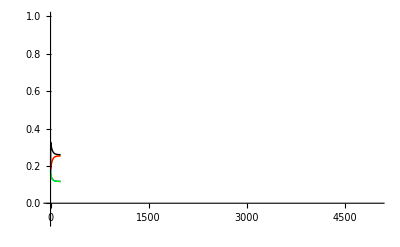

```mathematica
ListLinePlot[out[[5;;9]],PlotRange->{{0,5000},{-0.1,1.0}},PlotStyle->{Blue,Green,Yellow,Red,Black}]
```

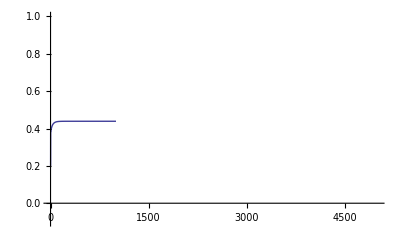

```mathematica
ListLinePlot[out[[9]],PlotRange->{{0,5000},{-0.1,1}}]
```

OK works.